# Integrating git with the Wolfram Language

## John Fultz, Wolfram Research, Inc. -Graphics- — jfultz

Join the Conversation #WolframTechConf

## What is git?

Sorry, this is the 60-second-intro-that-probably-still-leaves-you-lost version if you haven’t been exposed to it before...

### Version control system

### Decentralized

### Represents commits, directories, and files relationally in a directed acyclic graph

### Repos contain an object store, where the objects being stored are:

### • Commits

### • Trees

### • Blobs

### Object store is indexed by hexadecimal hashes known as SHAs

## What is git — a visualization

```mathematica
SetDirectory[NotebookDirectory[]];
Manipulate[GitGraph[GitOpen["repos/TalkRepo.git"],selector],{selector,{"Commits","Trees","Blobs"}}]
```

## Why access git from the Wolfram Language?

### A natural extension of a symbolic language

### Language support for tooling is a known good

### Git is the leader in version control

### Want to be able to support merging of notebooks

### Turned out to be an invaluable internal tool

## A basic introduction

### Repo creation/acquisition

```mathematica
r=GitOpen["C:\\wolfram\\git\\GitLink"]
```

<|EmptyQ→False,UnbornHeadQ→False,BareQ→False,GitDirectory→C:\wolfram\git\GitLink\.git\,WorkingDirectory→C:\wolfram\git\GitLink\|>

```mathematica
rclone = GitClone["repos/TalkRepo.git","../TalkRepo"]
```

<|EmptyQ→False,UnbornHeadQ→False,BareQ→False,GitDirectory→C:\wolfram\git\tmp\TalkRepo\.git\,WorkingDirectory→C:\wolfram\git\tmp\TalkRepo\|>

```mathematica
rnew = GitInit["../NewRepo"]
```

<|EmptyQ→True,UnbornHeadQ→True,BareQ→False,GitDirectory→C:\wolfram\git\tmp\NewRepo\.git\,WorkingDirectory→C:\wolfram\git\tmp\NewRepo\|>

## A basic introduction

### What can you do with a repo?

Get its properties:

```mathematica
GitProperties[rnew]
```

<|ShallowQ→False,EmptyQ→True,UnbornHeadQ→True,BareQ→False,GitDirectory→C:\wolfram\git\tmp\NewRepo\.git\,WorkingDirectory→C:\wolfram\git\tmp\NewRepo\,DetachedHeadQ→False,Namespace→$Failed,State→None,Conflicts→{},Remotes→<||>,LocalBranches→{},RemoteBranches→{},Tags→{}|>

See its status:

```mathematica
GitStatus[rnew]
```

<|New→{},Modified→{},Deleted→{},TypeChange→{},IndexNew→{},IndexModified→{},IndexDeleted→{},IndexTypeChange→{}|>

Add changes and commit changes:

```mathematica
Put[Sqrt[2],FileNameJoin[{rnew["WorkingDirectory"],"radical.wl"}]];
```

```mathematica
GitAdd[rnew,"radical.wl"]
```

{radical.wl}

```mathematica
c=GitCommit[rnew, "Added a radical"]
```

Commit: 65fc91a0…

Get information on commits:

```mathematica
GitProperties[c]
```

<|Type→Commit,Parents→{},Tree→Tree: 7d08bd39…,Author→<|Name→John Fultz,Email→jfultz@wolfram.com,TimeStamp→Thu 22 Oct 2015 07:47:26GMT-5.|>,Committer→<|Name→John Fultz,Email→jfultz@wolfram.com,TimeStamp→Thu 22 Oct 2015 07:47:26GMT-5.|>,SHA→65fc91a0e48c5ed5965336ab831f6ca4db8fb23a,Message→Added a radical|>

Release resources:

```mathematica
GitClose[rnew]
```

## Some more advanced concepts...

### Accessing arbitrary revisions

```mathematica
ToGitObject["master",r]
```

Commit: 8386bc60…

```mathematica
GitRange[r,"master"]//Short
```

{Commit: 8386bc60…,«271»,Commit: 42b1894a…}

```mathematica
GitRange[r,"origin/feature/StandardNotebookMerge", Not["master"]]
```

{Commit: d86376c0…,Commit: 9fdd4975…,Commit: 56368747…,Commit: 900f18c9…}

```mathematica
GitGraph[%,"Commits"]
```

## Some more advanced concepts...

### Accessing trees and blobs

```mathematica
GitExpandTree[ToGitObject["master",r]]
```

{<|Type→Blob,Object→Blob: f6efb46c…,Root→,Name→.gitLink.sublime-project,FileMode→Blob|>,<|Type→Blob,Object→Blob: b881e6d3…,Root→,Name→.gitignore,FileMode→Blob|>,<|Type→Tree,Object→Tree: bfab105f…,Root→,Name→GitLink,FileMode→Tree|>,<|Type→Tree,Object→Tree: facd4060…,Root→,Name→scripts,FileMode→Tree|>,<|Type→Tree,Object→Tree: 264cfef2…,Root→,Name→src,FileMode→Tree|>,<|Type→Tree,Object→Tree: 86fe6335…,Root→,Name→tests,FileMode→Tree|>}

```mathematica
GitReadBlob[%[[2,"Object"]]]
```

Components
LibraryResources
.project
*.sublime-workspace
.tags*

## So what can we do with it?

### Let’s do something practical...get some line counts

```mathematica
#Object&/@Select[GitExpandTree[ToGitObject["master",r]["Tree"],Infinity],StringMatchQ[#Name,__~~(".cpp"|".h")]&]
```

{Blob: f8b8c3fb…,Blob: 76928f47…,Blob: d451703a…,Blob: 7a1d7263…,Blob: 4b2793cb…,Blob: 79f08838…,Blob: 6d50e864…,Blob: 1179a38e…,Blob: 8b65e3c9…,Blob: f014a710…,Blob: 8a4931e8…,Blob: acf1b57b…,Blob: d3fc874c…,Blob: c4286885…,Blob: 11a4082a…,Blob: d6db86b9…,Blob: fe134205…,Blob: 60cd2b1a…,Blob: a587b9ca…,Blob: 9924ee2f…,Blob: eed85450…,Blob: 457d9423…,Blob: a7c43ecb…,Blob: f52a84f5…,Blob: eba8d6a7…,Blob: 80834e3f…,Blob: 370ea867…,Blob: 968fb4e2…,Blob: 8cebfa37…,Blob: 215ba4dc…,Blob: 0ca654cf…,Blob: 9be93dd5…,Blob: 037cd23b…,Blob: efa1bf8a…,Blob: 5a2ea714…,Blob: e63a181c…,Blob: a7e484b0…,Blob: e6bb5cef…,Blob: c83a1d74…,Blob: 60d5a03e…,Blob: 8708f49f…}

## So what can we do with it?

### Let’s do something practical...get some line counts

```mathematica
Clear[gitLineCount];
gitLineCount[commit_GitObject,pattern_]:=gitLineCount[Select[GitExpandTree[commit["Tree"],Infinity],StringMatchQ[#Name,pattern]&][[All,"Object"]]]/;GitType[commit]==="Commit"
gitLineCount[blobs:{___GitObject}]:=Total[gitLineCount/@blobs]
gitLineCount[blob_GitObject]:=(gitLineCount[blob]=Length[StringSplit[GitReadBlob[blob],"\n"]])/;GitType[blob]==="Blob"
```

```mathematica
gitLineCount[ToGitObject["HEAD",r],__~~(".cpp"|".h")]
```

5537

## Line counts

### This is easy!

```mathematica
es=EventSeries[{#["Author"]["TimeStamp"], gitLineCount[#,__~~(".cpp"|".h")]}&/@GitRange[r,"master"]]
```

EventSeries[…]

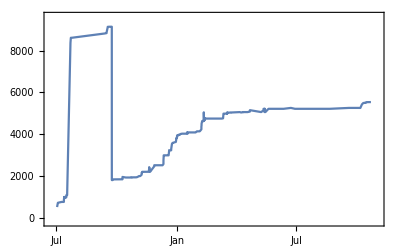

```mathematica
DateListPlot[es]
```

## Line counts

### Foiled by some messy data...what to do?

```mathematica
outliers=Select[GitRange[r,"master"],gitLineCount[#,__~~(".cpp"|".h")]>6000&]
```

{Commit: 3dfc8e4b…,Commit: e1e3d92d…,Commit: 1779b92d…,Commit: 3edcd406…,Commit: 7ade57be…,Commit: bb5e1a45…,Commit: 8985788d…,Commit: 8af6510c…,Commit: 9834d474…,Commit: 32da58fa…,Commit: 7aa732f6…,Commit: 949cca1e…}

```mathematica
Grid[{#Name, gitLineCount[#Object]}&/@Select[GitExpandTree[outliers[[1]],Infinity],StringMatchQ[#Name,__~~(".cpp"|".h")]&]]
```

GitLinkCommit.cpp | 204
GitLinkCommit.h | 43
GitLinkCommitRange.cpp | 88
GitLinkCommitRange.h | 28
GitLinkRepository.cpp | 392
GitLinkRepository.h | 63
GitLinkSuperClass.h | 23
MLHelper.cpp | 216
MLHelper.h | 65
WolframLibrary.h | 265
mathlink.h | 7074
CherryPickInterface.cpp | 82
CherryPickInterface.h | 14
CommitInterface.cpp | 71
CommitInterface.h | 14
Message.cpp | 33
Message.h | 35
RefInterface.cpp | 144
RepoInterface.cpp | 157
RepoInterface.h | 31
gitLink.cpp | 70
gitLink.h | 17
gitLinkPriv.h | 14

## Line counts

### Final solution...clean up the outliers

```mathematica
es=EventSeries[{#["Author"]["TimeStamp"], gitLineCount[#,__~~(".cpp"|".h")]-gitLineCount[#,"mathlink.h"]-gitLineCount[#,"WolframLibrary.h"]}&/@GitRange[r,"master"]]
```

EventSeries[…]

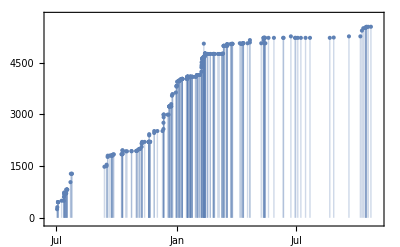

```mathematica
DateListPlot[es,Joined->False,Filling->Axis]
```

## More fun with GitLink

### A branch browser (how many languages can build this in 13 lines of code?)

```mathematica
icon=-Graphics-;
gitBrowse[tree_GitObject] := DynamicModule[{item},Row[{ListPicker[Dynamic[item],#Object->(#Name<>If[#Type==="Tree","»",""])&/@GitExpandTree[tree],Multiselection->False,ImageSize->{150,300}],Dynamic[gitBrowse[item]]}]] /; GitType[tree]==="Tree";
gitBrowse[blob_GitObject] :=
Button[icon,NotebookPut[GitReadBlob[blob,"NB"]],Method->"Queued"]/;GitType[blob]==="Blob";
gitBrowse[{}]:=""
gitBrowse[{item_}]:=gitBrowse[item]
gitBrowse[repo_GitRepo]:=
Deploy@DynamicModule[{branch=repo["HeadBranch"]},Column[{
PopupMenu[Dynamic[branch],repo["LocalBranches"]],
Dynamic@gitBrowse[ToGitObject[branch,repo]["Tree"]]}]]
```

```mathematica
gitBrowse[r]
```

## [He’s showing off now...]

### A branch browser with differencing

#### Code

```mathematica
Clear[objectMatchingName,colorizeLabel]
objectMatchingName[name_,list_]:=#Object&/@Select[#Name===name&][list]/.{x_GitObject}:>x
colorizeLabel[objs_List->label_]:=objs->Style[label,Switch[objs,
{x_GitObject,x_GitObject},Black,
{_GitObject,_GitObject},Orange,
{None,_GitObject},Darker[Green],
{_GitObject,None},Blue]];
```

```mathematica
Clear[diffBrowse,diffItemList]
diffItemList[{tree1_GitObject, tree2_GitObject}]:=
Module[{list1=GitExpandTree[tree1], list2=GitExpandTree[tree2],results},
results= Union[#Name&/@list1,#Name&/@list2];
results={objectMatchingName[#,list1],objectMatchingName[#,list2]}->#&/@results;
results= results /. {}->None;
colorizeLabel/@results];

diffBrowse[{tree1_GitObject, tree2_GitObject}]:=
DynamicModule[{item},Row[{ListPicker[Dynamic[item],diffItemList[{tree1, tree2}],Multiselection->False,ImageSize->{150,300}],Dynamic[diffBrowse[Flatten[item]]]},""]] /; GitType[tree1] === "Tree" && GitType[tree2] === "Tree" && tree1 =!= tree2;
diffBrowse[{blob1_GitObject, blob2_GitObject}]:=
DynamicModule[{item},Button[Row[{icon,Style["⇔",24],icon}],NotebookPut@NotebookTools`NotebookDiff[GitReadBlob[blob1,"NB"],GitReadBlob[blob2,"NB"]]]] /; GitType[blob1] === "Blob" && GitType[blob2] === "Blob" && blob1 =!= blob2;

diffBrowse[{___, obj_GitObject, ___}]:=gitBrowse[obj];

diffBrowse[{}] := "";

diffBrowse[repo_GitRepo]:=
Deploy@DynamicModule[{branch1,branch2},
Column[{
Row[{PopupMenu[Dynamic[branch1],repo["LocalBranches"],MenuStyle->{14,Bold,Blue}],
PopupMenu[Dynamic[branch2],repo["LocalBranches"],MenuStyle->{14,Bold,Darker[Green]}]},""],
Dynamic@diffBrowse[{ToGitObject[branch1,repo]["Tree"],ToGitObject[branch2,repo]["Tree"]}]
}]]
```

#### Demo

```mathematica
diffBrowse[r]
```

## But it solved real problems for us

### Post-processing repos migrated from cvs

### Random git scriptability needs (e.g., let’s find all named and fully merged feature branches and clean them up)

### Implementing a multi-repo management tool

### Doing automated merge deployments of development branches (how we avoid having to have a “develop” branch slowing down our releases)

## We built a thing...

### Yummy, yummy dog food. 50+ developers use this every day at Wolfram.

## And...

### 3-way notebook merging...

```mathematica
mergeRepo=GitClone["repos/MergeRepo.git","../MergeRepo"];
NotebookOpen[AbsoluteFileName["..\\MergeRepo\\Demo.nb"]];
```

```mathematica
GitCheckoutReference[mergeRepo,GitMergeBase[mergeRepo,"master","origin/feature_branch"]]
```

Commit: f61e9228…

```mathematica
GitCheckoutReference[mergeRepo, "master"]
```

Commit: c41e3e3d…

```mathematica
GitCheckoutReference[mergeRepo,"origin/feature_branch"]
```

Commit: 5eafca70…

```mathematica
GitCheckoutReference[mergeRepo,"master"];
GitMerge[mergeRepo,"origin/feature_branch"]
```

Commit: 1130d9e6…

## When’s it shipping?

### A large amount is already done

### We need to get some more coverage of git functionality

### Some details may change before we ship. I’ll update this talk to reflect any changes.

## Update? But where would we find it?

## Github, of course!

### https://github.com/WolframResearch

### This is repo #1. More to follow.